```mathematica
u=.
```

```mathematica
v=.
```

```mathematica
w=.
```

```mathematica
V0={1,1}
```

{1,1}

```mathematica
V1={2,3}
```

{2,3}

```mathematica
V2={2,6}
```

{2,6}

```mathematica
V3={1,10}
```

{1,10}

```mathematica
E0=V1-V0
```

{1,2}

```mathematica
E1=V2-V1
```

{0,3}

```mathematica
E2=V3-V2
```

{-1,4}

```mathematica
E3=V0-V3
```

{0,-9}

```mathematica
N0={-E0[[2]],E0[[1]]}
```

{-2,1}

```mathematica
N1={-E1[[2]],E1[[1]]}
```

{-3,0}

```mathematica
N2={-E2[[2]],E2[[1]]}
```

{-4,-1}

```mathematica
N3={-E3[[2]],E3[[1]]}
```

{9,0}

```mathematica
r=2
```

2

```mathematica
P={u,v,w}
```

{u,v,w}

```mathematica
R0={u,v}
```

{u,v}

```mathematica
R1={u+w,v}
```

{u+w,v}

```mathematica
R2={u+w,v+w/r}
```

{u+w,v+w/2}

```mathematica
R3={u,v+w/r}
```

{u,v+w/2}

```mathematica
temp0=Expand[N[Dot[N0,R1-V0]]]
```

1.-2. u+v-2. w

```mathematica
M0={Coefficient[temp0,u],Coefficient[temp0,v],Coefficient[temp0,w]}
```

{-2.,1,-2.}

```mathematica
c0=-(temp0-Dot[M0,{u,v,w}])
```

-1.

```mathematica
temp1=Expand[N[Dot[N1,R1-V1]]]
```

6.-3. u-3. w

```mathematica
M1={Coefficient[temp1,u],Coefficient[temp1,v],Coefficient[temp1,w]}
```

{-3.,0,-3.}

```mathematica
c1= -(temp1-Dot[M1,{u,v,w}])
```

-6.

```mathematica
temp2=Expand[N[Dot[N2,R2-V2]]]
```

14.-4. u-1. v-4.5 w

```mathematica
M2={Coefficient[temp2,u],Coefficient[temp2,v],Coefficient[temp2,w]}
```

{-4.,-1.,-4.5}

```mathematica
c2=-(temp2-Dot[M2,{u,v,w}])
```

-14.

```mathematica
temp3=Expand[N[Dot[N3,R0-V3]]]
```

-9.+9. u

```mathematica
M3={Coefficient[temp3,u],Coefficient[temp3,v],Coefficient[temp3,w]}
```

{9.,0,0}

```mathematica
c3=-(temp3-Dot[M3,{u,v,w}])
```

9.

```mathematica
NMaximize[{w,Dot[N0,R1-V0]>=0 &&Dot[N1,R1-V1]>=0&&Dot[N2,R2-V2]>=0&&Dot[N3,R0-V3]>=0},{u,v,w}]
```

{1.,{u→1.,v→5.5,w→1.}}

```mathematica
M0xM2=Cross[M0,M2]
```

{-6.5,-1.,6.}

```mathematica
det02=Dot[M0xM2,M0xM2]
```

79.25

```mathematica
dot00=Dot[M0,M0]
```

9.

```mathematica
dot02=Dot[M0,M2]
```

16.

```mathematica
dot22=Dot[M2,M2]
```

37.25

```mathematica
a0=(dot22*c0-dot02*c2)/det02
```

2.35647

```mathematica
a2=(dot00*c2-dot02*c0)/det02
```

-1.38801

```mathematica
K02=a0*M0+a2*M2
```

{0.839117,3.74448,1.53312}

```mathematica
alpha1=Dot[M1,M0xM2]
```

1.5

```mathematica
beta1=Dot[M1,K02]-c1
```

-1.11672

```mathematica
alpha3=Dot[M3,M0xM2]
```

-58.5

```mathematica
beta3=Dot[M3,K02]-c3
```

-1.44795

```mathematica
M1xM3=Cross[M1,M3]
```

{0.,-27.,0.}

```mathematica
det13=Dot[M1xM3,M1xM3]
```

729.

```mathematica
dot11=Dot[M1,M1]
```

18.

```mathematica
dot13=Dot[M1,M3]
```

-27.

```mathematica
dot33=Dot[M3,M3]
```

81.

```mathematica
a1=(dot33*c1-dot13*c3)/det13
```

-0.333333

```mathematica
a3=(dot11*c3-dot13*c1)/det13
```

0.

```mathematica
K13=a1*M1+a3*M3
```

{1.,0.,1.}

```mathematica
nm=NMaximize[{w,
Dot[N0,R0-V0]>=0&&Dot[N0,R1-V0]>=0&&Dot[N0,R2-V0]>=0 &&Dot[N0,R3-V0]>=0&&
Dot[N1,R0-V1]>=0&&Dot[N1,R1-V1]>=0&&Dot[N1,R2-V1]>=0 &&Dot[N1,R3-V1]>=0&&
Dot[N2,R0-V2]>=0&&Dot[N2,R1-V2]>=0&&Dot[N2,R2-V2]>=0 &&Dot[N2,R3-V2]>=0&&
Dot[N3,R0-V3]>=0&&Dot[N3,R1-V3]>=0&&Dot[N3,R2-V3]>=0 &&Dot[N3,R3-V3]>=0},{u,v,w}][[2]][[All,2]]
```

{1.,3.,1.}

```mathematica
u=nm[[1]]
```

1.

```mathematica
v=nm[[2]]
```

3.

```mathematica
w=nm[[3]]
```

1.

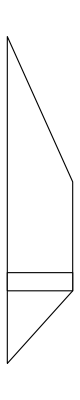

```mathematica
Show[
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{V0,V1,V2,V3}]}],
Graphics[{EdgeForm[Black],FaceForm[White],Polygon[{R0,R1,R2,R3}]}]
]
```